# Practical Codes for Storage Systems

# An Introduction to Entanglement Codes

Entanglement codes generate redundant information to protect content against failures in a storage system. The method increases system reliability and also improves performance. Internally, it builds multiple paths to read data using combinations of elements stored in the system.
This tutorial introduces simple entanglement codes.

## Simple Entanglement Codes

Simple entanglements create chains of interdependent elements that alternate plain and encoded data. In this model, data is represented using a vertex and encoded data (redundant information, sometimes named as parities) is represented using an edge. The chain grows by adding elements at the right extremity. When a vertex is added to the chain, its content is XORed with the content of the last edge. For example, imagine that the last vertex in a chain is 3. The next vertex added to the system will be assigned to the position 4. Each vertex that is added to the system generates an outgoing edge. This edge is computed by XORing the content of the new vertex 4 and the edge that connects both vertices (edge 3 -> 4). The output is the encoded data that generates edge 4 -> 5 and it will be used as the input for the next encoding when the vertex (5) is added to the chain.

A visualization of an open entanglement chain of length 5 (we only count the vertices that contain information). The first and last vertices are virtual elements and do not contain information. The first vertex contains the initial condition of the chain. The last vertex is needed for the existence of edge 5 -> 6. The content of vertex 6 will be replaced by the real information when additional data is inserted to the system:

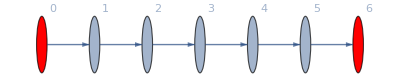

```mathematica
g=Graph[{0 ->1,1->2,2->3,3->4, 4->5,5->6},VertexLabels->"Name",VertexSize->Medium, VertexStyle -> {0 ->Red,6->Red}]
```

### Write data

Vertices represent data. They can store anything, e.g. a digit, numbers, chars, strings or large chunks of data. The only constraint is that all of them must store the same amount of information.

In this example, the chain will store “Hello”. First, we convert the string to character codes:

```mathematica
vertexValues=ToCharacterCode["Hello"]
```

{72,101,108,108,111}

The encoder uses the function BitXor to compute the bitwise XOR of the last two elements of the chain. The input are the vertex being encoded and its incident edge (whose weight was generated during the encoding of its predecessor vertex and contains redundant information derived from all the predecessor vertices).

If the vertex values is known, the encoding process is equivalent to compute the cumulative bitwise XOR operations of the elements of the vertexValues list:

```mathematica
encodedData= FoldList[BitXor,0,vertexValues]
```

{0,72,45,65,45,66}

The list of vertexValues only contains the values for vertices 1-5. Let’s fix it.

To fill the virtual vertices with some content, we add zeros at the first and last position of the list:

```mathematica
vertexValues= Insert[vertexValues,0,{{1},{-1}}]
```

{0,72,101,108,108,111,0}

Now, we can redefine the graph using the new content.

We could describe vertices with associations. The key is the index/label of the vertex and the value contains one element of the vertexValues list:

```mathematica
vertex = AssociationThread[VertexList[g],vertexValues]
```

<|0→0,1→72,2→101,3→108,4→108,5→111,6→0|>

We can visualize the entanglement chain using the vertex weight to store plain data and edge weight to store encoded data:

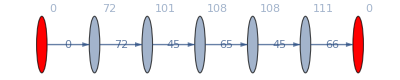

```mathematica
g=Graph[{0->1,1->2,2->3,3->4, 4->5,5->6},VertexSize->Medium,VertexStyle -> {0 ->Red,6->Red},VertexWeight->vertexValues,EdgeWeight-> encodedData,VertexLabels->"VertexWeight",EdgeLabels-> "EdgeWeight"]
```

### Read data

Data can be recovered using nodes or edges

Method 1: Reading plain text from vertices (without decoding)

```mathematica
Row[FromCharacterCode[PropertyValue[{g,#},VertexWeight]]&/@{1,2,3,4,5}]
```

Hello

Method 2: Decoding data from edges. We apply BitXor to pair of values obtained by Partition.

```mathematica
FromCharacterCode[BitXor@@@Partition[encodedData,2,1]]
```

Hello

### Decoding in detail

We can read the content of a node by applying the bitwise XOR to the weight of its two adjacent edges

For example, to read “e” (char code 101) we use the adjacent edges that contain 72 and 45.

```mathematica
FromCharacterCode[BitXor[encodedData[[2]],encodedData[[3]]]]
```

e

We can also recompute the value of an edge. There are two ways depending on the direction we are moving on the chain. In this example, we recomputed encodedData[[3]]:

Moving from left to right:

```mathematica
BitXor[encodedData[[2]],vertexValues[[3]]]
```

45

Moving from right to left:

```mathematica
BitXor[encodedData[[4]],vertexValues[[4]]]
```

45

## Failure Patterns

There are three type of failures that this structure cannot tolerate. That means that it is not possible to recover the information inside the erasure pattern if the failure occurs.

Type A Failures: This failure only occurs if the last two elements of the chain are not available (without considering the virtual node 6).

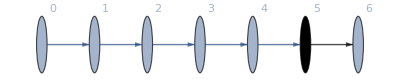

```mathematica
Graph[{0 ->1,1->2,2->3,3->4, 4->5,5->6},VertexLabels->"Name",VertexSize->Medium, EdgeStyle->{(5-> 6)-> Black},VertexStyle -> {5 ->Black}]
```

Type B Failures: This failure occurs at any location of the chain and is composed by a node, and edge and its neighbor node.

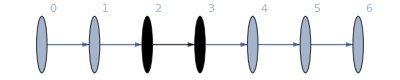

```mathematica
Graph[{0 ->1,1->2,2->3,3->4, 4->5,5->6},VertexLabels->"Name",VertexSize->Medium, EdgeStyle->{(2-> 3)-> Black},VertexStyle -> {2 ->Black,3->Black}]
```

Type C Failures: This failure occurs at any location of the chain. It is basically an expanded version of type B failure, where the nodes are located at more than one hop and all the edges between the nodes are not available too.

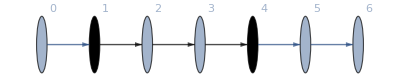

```mathematica
Graph[{0 ->1,1->2,2->3,3->4, 4->5,5->6},VertexLabels->"Name",VertexSize->Medium, EdgeStyle->{(1-> 2)-> Black,(2-> 3)-> Black,(3-> 4)-> Black},VertexStyle -> {1 ->Black,4->Black}]
```

Authorship information

Vero Estrada-Galinanes

23-Jun-2017
References: Estrada-Galinanes, Vero, Jehan-François Pâris, and Pascal Felber. “Simple data entanglement layouts with high reliability.” Performance Computing and Communications Conference (IPCCC), 2016 IEEE 35th International. IEEE, 2016.

estrada (.) veronica (@) gmail (.) com